```mathematica
(*ArcTan[(x-5)^2]*)
```

## Benchmark

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"];
```

#### Comparison with GaussNumber

```mathematica
Gauss[n_,a_,b_]:=Module[{aux,Wivec,fvec, valor},
(*"n" representa o número de pontos de integração*)
aux=SetPrecision[GaussianQuadratureWeights[n,a,b],MachinePrecision];
Wivec=aux[[All,2]];
fvec=aux[[All,1]];
For[i=1,i≤ Length[fvec],i++,
fvec[[i]]=f[fvec[[i]]];
];
valor=fvec.Wivec;
Return[valor];
];
```

```mathematica
GaussNumber[a_,b_]:=Module[{n,Optimal}, 
n=1;
While[Abs[Gauss[n,a,b]-Gauss[n+1,a,b]]>10^-10,If[n<9,Optimal=n,Break[]];n++];
Optimal=n;
Return [Optimal];(*Return the number of integration points*)
]
```

#### Initial Data

```mathematica
a=-10; (*Menor limite de integração*)
b=10;(*Maior limite de integração*)
e=0.25; (*espaçamento*)
c5=Table[a+i*e  -e ->  a+i*e ,{i,1,(b-a)*(1/e)}];
ϵd=10^-3; 
(*apox da derivada*)
maxavailable=10;
```

```mathematica
f[x_]=ArcTan[(x-5)^2]+Sin[x];
```

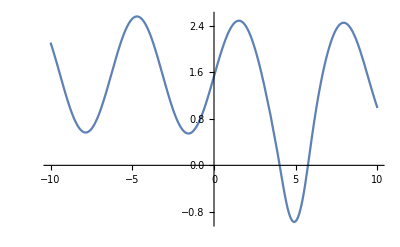

```mathematica
Plot[f[x],{x,a,b},PlotRange->All]
```

## Method considering derivates

#### Numerical Derivative:

```mathematica
(*First derivate approximation*)
```

```mathematica
dfdx1[x_]:=Module[{derivate},
derivate=(f[x+ϵd]-f[x-ϵd])/(2ϵd);
Return[Abs[derivate]//N];
]
```

```mathematica
(*Second derivate approximation*)
```

```mathematica
dfdx2[x_]:=Module[{derivate},
derivate=(dfdx1[x+ϵd]-dfdx1[x-ϵd])/(2ϵd);
Return[Abs[derivate]//N];
]
```

```mathematica
(*Third derivate approximation*)
```

```mathematica
dfdx3[x_]:=Module[{derivate},
derivate=(dfdx2[x+ϵd]-dfdx2[x-ϵd])/(2ϵd);
Return[Abs[derivate]//N];
]
```

```mathematica
(*Fourfth derivate approximation*)
```

```mathematica
dfdx4[x_]:=Module[{derivate},
derivate=(dfdx3[x+ϵd]-dfdx3[x-ϵd])/(2ϵd);
Return[Abs[derivate]//N];
]
```

```mathematica
(*Fifth derivate approximation*)
```

```mathematica
dfdx5[x_]:=Module[{derivate},
derivate=(dfdx4[x+ϵd]-dfdx4[x-ϵd])/(2ϵd);
Return[Abs[derivate]//N];
]
```

```mathematica
Partial[x_]:=Module[{β,fx},
β=ϵd;
fx=Catch[If[dfdx1[x]<β,Throw[1],
	If[dfdx2[x]<β,Throw[1],
	If[dfdx3[x]<β,Throw[2],
	If[dfdx4[x]<β,Throw[2],
	If[dfdx5[x]<β,Throw[3],Throw[maxavailable]]]]]]];
Return[fx];
];
```

#### Derivative Analysis:

```mathematica
(*Not using derivates approximations*)
```

```mathematica
DerivateAnalisysd1[a1_,b1_]:=Module[{a,b,min, max,aux,ref0,ref,diferenced1},
a=Min[a1,b1];
b=Max[a1,b1];
(*Retorna a diferença entre o maior e o menor valor absoluto da primeira derivada da função f[x] para o intervalo (a,b)*)
min=max=dfdx1[a];
aux=5;
For[i=0,i≤aux,i++;ref=dfdx1[a+i*(b-a)/aux];
If[ref<min ,min=ref];
If[ref>max,max=ref];
];
(*Finds the min and max value for second derivate*)
diferenced1=max-min;
Return[diferenced1]//N
]
```

```mathematica
DerivateAnalisysd2[a1_,b1_]:=Module[{a,b,min, max,aux,ref,diferenced2},
a=Min[a1,b1];
b=Max[a1,b1];
(*Retorna a diferença entre o maior e o menor valor absoluto da segunda derivada da função f[x] para o intervalo (a,b)*)
min=max=dfdx2[a];
aux=5;
For[i=0,i≤aux,i++;ref=dfdx2[a+i*(b-a)/aux];
If[ref<min ,min=ref];
If[ref>max,max=ref];
];
(*Finds the min and max value for second derivate*)
diferenced2=max-min;
Return[diferenced2//N];
]
```

#### Gauss Number 2

```mathematica
GaussNumberII[x0_,x1_]:=Module[{n,Optimal, α=Abs[b-a],maxintorder,minintorder,result,test}, 
ϵ=Exp[-α/Abs[x0-x1]]; (*quanto menor o intervalo, menor sera o valor de ϵ (mais perto de zero), e quanto menor ϵ, menos pontos de integração serão necessários*)
maxintorder=Max[Partial[x0],Partial[x1]];
minintorder=Min[Partial[x0],Partial[x1]];
minintorder=If[minintorder<maxavailable,minintorder,3(*caso os dois pontos retornem dfdx5>β*)];
dfdx=DerivateAnalisysd1[x0,x1]; 
df2dx2=DerivateAnalisysd2[x0,x1];
n=IntegerPart[Exp[(df2dx2)/(dfdx+10^-15)]];
Optimal=IntegerPart[n];
result=If[Optimal<minintorder,minintorder,If[Optimal>maxintorder,maxintorder,Optimal]];
Return[result];
];
```

```mathematica
ComparisonIntegrate[x0_,x1_]:=Module[{gn1,nint},
gn1=Gauss[GaussNumberII[x0,x1],x0,x1];
nint=NIntegrate[f[x],{x,x0,x1}];
Return[gn1-nint]//N;
]
```

```mathematica
TableForm[Table[GaussNumber[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}],TableHeadings-> {c5,{"Gauss"}}]&&
TableForm[Table[GaussNumberII[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}],TableHeadings-> {{},{"metodo novo"}}]&&
TableForm[Table[ComparisonIntegrate[(a+i*e)-e,a+i*e],{i,1,(b-a)*(1/e)}],TableHeadings-> {{},{"d2"}}]
(*Variação por espaço do subintervalo!*)
```

-10.→-9.75 | 3
-9.75→-9.5 | 3
-9.5→-9.25 | 3
-9.25→-9. | 3
-9.→-8.75 | 3
-8.75→-8.5 | 3
-8.5→-8.25 | 3
-8.25→-8. | 3
-8.→-7.75 | 3
-7.75→-7.5 | 3
-7.5→-7.25 | 3
-7.25→-7. | 3
-7.→-6.75 | 3
-6.75→-6.5 | 3
-6.5→-6.25 | 3
-6.25→-6. | 3
-6.→-5.75 | 3
-5.75→-5.5 | 3
-5.5→-5.25 | 3
-5.25→-5. | 3
-5.→-4.75 | 3
-4.75→-4.5 | 3
-4.5→-4.25 | 3
-4.25→-4. | 3
-4.→-3.75 | 3
-3.75→-3.5 | 3
-3.5→-3.25 | 3
-3.25→-3. | 3
-3.→-2.75 | 3
-2.75→-2.5 | 3
-2.5→-2.25 | 3
-2.25→-2. | 3
-2.→-1.75 | 3
-1.75→-1.5 | 3
-1.5→-1.25 | 3
-1.25→-1. | 3
-1.→-0.75 | 3
-0.75→-0.5 | 3
-0.5→-0.25 | 3
-0.25→0. | 3
0.→0.25 | 3
0.25→0.5 | 3
0.5→0.75 | 3
0.75→1. | 3
1.→1.25 | 3
1.25→1.5 | 3
1.5→1.75 | 3
1.75→2. | 3
2.→2.25 | 3
2.25→2.5 | 3
2.5→2.75 | 3
2.75→3. | 3
3.→3.25 | 3
3.25→3.5 | 4
3.5→3.75 | 4
3.75→4. | 4
4.→4.25 | 5
4.25→4.5 | 5
4.5→4.75 | 4
4.75→5. | 4
5.→5.25 | 4
5.25→5.5 | 4
5.5→5.75 | 5
5.75→6. | 5
6.→6.25 | 4
6.25→6.5 | 4
6.5→6.75 | 4
6.75→7. | 3
7.→7.25 | 3
7.25→7.5 | 3
7.5→7.75 | 3
7.75→8. | 3
8.→8.25 | 3
8.25→8.5 | 3
8.5→8.75 | 3
8.75→9. | 3
9.→9.25 | 3
9.25→9.5 | 3
9.5→9.75 | 3
9.75→10. | 3&& | 9
 | 10
 | 10
 | 10
 | 4
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 4
 | 10
 | 10
 | 10
 | 8
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 7
 | 10
 | 10
 | 10
 | 5
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 4
 | 10
 | 10
 | 10
 | 10
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 10
 | 10
 | 10
 | 3
 | 3
 | 3
 | 3
 | 10
 | 10
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 3
 | 5
 | 10
 | 10
 | 10
 | 7&& | -5.55112×10^-16
 | -4.996×10^-16
 | -3.88578×10^-16
 | -3.88578×10^-16
 | 8.88178×10^-16
 | -2.17033×10^-11
 | -2.62457×10^-11
 | -2.91563×10^-11
 | -3.02542×10^-11
 | -2.9471×10^-11
 | -2.68554×10^-11
 | -2.25701×10^-11
 | 9.4369×10^-16
 | -4.44089×10^-16
 | -4.44089×10^-16
 | -5.55112×10^-16
 | -4.996×10^-16
 | 1.85103×10^-11
 | 2.38578×10^-11
 | 2.7722×10^-11
 | 2.98627×10^-11
 | 3.01469×10^-11
 | 2.85567×10^-11
 | 2.51914×10^-11
 | 2.026×10^-11
 | -4.44089×10^-16
 | -6.10623×10^-16
 | -3.88578×10^-16
 | -3.88578×10^-16
 | -2.77556×10^-16
 | -2.09745×10^-11
 | -2.57089×10^-11
 | -2.88414×10^-11
 | -3.0176×10^-11
 | -2.96277×10^-11
 | -2.72277×10^-11
 | -2.31212×10^-11
 | 9.99201×10^-16
 | -3.33067×10^-16
 | -4.44089×10^-16
 | -5.55112×10^-16
 | -5.55112×10^-16
 | 1.87764×10^-11
 | 2.4914×10^-11
 | 3.00252×10^-11
 | 3.41814×10^-11
 | 3.78358×10^-11
 | 4.20639×10^-11
 | 4.88969×10^-11
 | 6.13471×10^-11
 | 8.03229×10^-11
 | 8.33009×10^-11
 | -8.49779×10^-11
 | -1.11696×10^-9
 | -4.24951×10^-9
 | -8.32667×10^-17
 | 5.55112×10^-17
 | 1.38778×10^-16
 | -7.70705×10^-9
 | 6.93046×10^-9
 | 6.9326×10^-9
 | -7.70077×10^-9
 | 6.245×10^-17
 | -8.32667×10^-17
 | -4.65792×10^-10
 | -4.23267×10^-9
 | -1.09982×10^-9
 | -6.85985×10^-11
 | 9.78989×10^-11
 | 9.22319×10^-11
 | 6.98264×10^-11
 | 5.34197×10^-11
 | 4.23487×10^-11
 | 3.38651×10^-11
 | 2.62018×10^-11
 | -5.55112×10^-16
 | -4.996×10^-16
 | -4.996×10^-16
 | -4.44089×10^-16
 | -2.22045×10^-16